## Data directories

```mathematica
DownloadDirectory="https://download.bhptoolkit.org/few/data/1PAT1R/";
```

```mathematica
Import[DownloadDirectory<>"Trajectory1PAT1R.h5"]
```

{/Energy/1PA/Grid,/Energy/1PA/dEdOmega,/Flux/AngularMomentum/0PA/Infinity,/Flux/AngularMomentum/0PA/Grid,/Flux/AngularMomentum/0PA/Horizon,/Flux/Energy/0PA/Infinity,/Flux/Energy/0PA/Grid,/Flux/Energy/0PA/Horizon,/Flux/Energy/1PA/Grid,/Flux/Energy/1PA/Infinity,/Flux/Energy/1PAchi1/Grid,/Flux/Energy/1PAchi1/Infinity,/Flux/Energy/1PAchi1/Horizon,/Flux/Energy/1PAchi2/Infinity,/Flux/Energy/1PAchi2/Grid,/Flux/Energy/1PAchi2/Horizon}

```mathematica
Import[DownloadDirectory<>"Amplitudes1PAT1R.h5"]
```

{/0PA/l3/m0/Infinity,/0PA/l3/m1/Infinity,/0PA/l3/m2/Infinity,/0PA/l3/m3/Infinity,/0PA/l2/m0/Infinity,/0PA/l2/m1/Infinity,/0PA/l2/m2/Infinity,/0PA/l4/m0/Infinity,/0PA/l4/m1/Infinity,/0PA/l4/m2/Infinity,/0PA/l4/m3/Infinity,/0PA/l4/m4/Infinity,/0PA/Grid,/0PA/l5/m0/Infinity,/0PA/l5/m1/Infinity,/0PA/l5/m2/Infinity,/0PA/l5/m3/Infinity,/0PA/l5/m4/Infinity,/0PA/l5/m5/Infinity,/1PA/l3/m0/Infinity,/1PA/l3/m1/Infinity,/1PA/l3/m2/Infinity,/1PA/l3/m3/Infinity,/1PA/l2/m0/Infinity,/1PA/l2/m1/Infinity,/1PA/l2/m2/Infinity,/1PA/l4/m0/Infinity,/1PA/l4/m1/Infinity,/1PA/l4/m2/Infinity,/1PA/l4/m3/Infinity,/1PA/l4/m4/Infinity,/1PA/Grid,/1PA/l5/m0/Infinity,/1PA/l5/m1/Infinity,/1PA/l5/m2/Infinity,/1PA/l5/m3/Infinity,/1PA/l5/m4/Infinity,/1PA/l5/m5/Infinity,/1PAchi1/l3/m0/Infinity,/1PAchi1/l3/m1/Infinity,/1PAchi1/l3/m2/Infinity,/1PAchi1/l3/m3/Infinity,/1PAchi1/Grid,/1PAchi1/l4/m0/Infinity,/1PAchi1/l4/m1/Infinity,/1PAchi1/l4/m2/Infinity,/1PAchi1/l4/m3/Infinity,/1PAchi1/l4/m4/Infinity,/1PAchi1/l2/m0/Infinity,/1PAchi1/l2/m1/Infinity,/1PAchi1/l2/m2/Infinity,/1PAchi1/l5/m0/Infinity,/1PAchi1/l5/m1/Infinity,/1PAchi1/l5/m2/Infinity,/1PAchi1/l5/m3/Infinity,/1PAchi1/l5/m4/Infinity,/1PAchi1/l5/m5/Infinity,/1PAchi2/l3/m0/Infinity,/1PAchi2/l3/m1/Infinity,/1PAchi2/l3/m2/Infinity,/1PAchi2/l3/m3/Infinity,/1PAchi2/l2/m0/Infinity,/1PAchi2/l2/m1/Infinity,/1PAchi2/l2/m2/Infinity,/1PAchi2/l4/m0/Infinity,/1PAchi2/l4/m1/Infinity,/1PAchi2/l4/m2/Infinity,/1PAchi2/l4/m3/Infinity,/1PAchi2/l4/m4/Infinity,/1PAchi2/Grid,/1PAchi2/l5/m0/Infinity,/1PAchi2/l5/m1/Infinity,/1PAchi2/l5/m2/Infinity,/1PAchi2/l5/m3/Infinity,/1PAchi2/l5/m4/Infinity,/1PAchi2/l5/m5/Infinity}

```mathematica
WaSABIdirectory=FileNameDrop[FindFile["WaSABI``"],-2];
WaSABIsfDataDirectory=FileNameJoin[{WaSABIdirectory,"InspiralModels"}];
```

```mathematica
Flux0PAdirectory = FileNameJoin[{WaSABIsfDataDirectory, "sf_data/1SF_Flux/Schwarz_Circ"}];
Flux1PAchi1Directory = FileNameJoin[{WaSABIsfDataDirectory, "sf_data/1SF_Flux/Linear_Kerr_Circ"}];
Flux1PAdirectory = FileNameJoin[{WaSABIsfDataDirectory, "sf_data/2SF_Flux/Schwarz_Circ"}];
Flux1PAchi2Directory = FileNameJoin[{WaSABIsfDataDirectory, "sf_data/Leading_S2_Flux/Schwarz_Circ"}];
Energy1PAdirectory = FileNameJoin[{WaSABIsfDataDirectory, "sf_data/1SF_Local_Invariants/Schwarz_Circ"}];
```

## 1PA energy

### Data and interpolants

```mathematica
Energy1PAGrid=Import[DownloadDirectory<>"Trajectory1PAT1R.h5","Energy/1PA/Grid"];
Energy1PAdEdOmegaData=Import[DownloadDirectory<>"Trajectory1PAT1R.h5","Energy/1PA/dEdOmega"];
Energy1PAdEdOmegaOnGrid=Transpose[{Energy1PAGrid,Energy1PAdEdOmegaData}];
```

```mathematica
Energy1PAdEdOmega=Interpolation[Energy1PAdEdOmegaOnGrid,InterpolationOrder->8];
```

```mathematica
WaSABIRedshiftData=Import[Energy1PAdirectory<>"/1SFCircSchwarzRedshfit.m"];
```

```mathematica
WaSABIz = Interpolation[WaSABIRedshiftData, InterpolationOrder->8];
```

```mathematica
WaSABIEnergy1PA[x_]:=(1/2 WaSABIz[x]-x/3WaSABIz'[x]-1+Sqrt[1-3x]+x/6  (7-24x)/(1-3x)^(3/2))
```

```mathematica
dxdΩ[x_]:=2/(3 Sqrt[x])
```

```mathematica
WaSABI1PAdEdOmega[r0_]:=dxdΩ[1/r0]WaSABIEnergy1PA'[1/r0];
```

```mathematica
rmin1PAEnergy=Energy1PAGrid[[1]]
rmax1PAEnergy=Energy1PAGrid[[-1]]
```

6.

29.9066

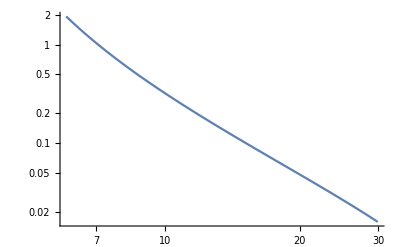

```mathematica
LogLogPlot[-Energy1PAdEdOmega[r0],{r0,rmin1PAEnergy,rmax1PAEnergy}]
```

### Comparison of interpolating functions

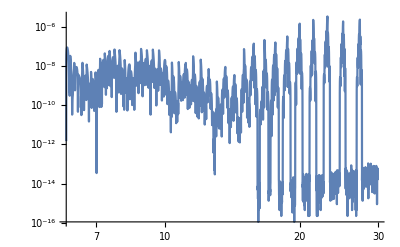

```mathematica
LogLogPlot[Abs[1-Energy1PAdEdOmega[r0]/WaSABI1PAdEdOmega[r0]],{r0,rmin1PAEnergy,rmax1PAEnergy}]
```

## 0PA energy flux

### Data and interpolants

```mathematica
FluxEnergy0PAGrid=Import[DownloadDirectory<>"Trajectory1PAT1R.h5","Flux/Energy/0PA/Grid"];
FluxEnergy0PAInfinityData=Import[DownloadDirectory<>"Trajectory1PAT1R.h5","Flux/Energy/0PA/Infinity"];
FluxEnergy0PAHorizonData=Import[DownloadDirectory<>"Trajectory1PAT1R.h5","Flux/Energy/0PA/Horizon"];
```

```mathematica
FluxEnergy0PAInfinityOnGrid=Transpose[{FluxEnergy0PAGrid,FluxEnergy0PAInfinityData}];
FluxEnergy0PAHorizonOnGrid=Transpose[{FluxEnergy0PAGrid,FluxEnergy0PAHorizonData}];
```

```mathematica
FluxEnergy0PAInfinity=Interpolation[FluxEnergy0PAInfinityOnGrid,InterpolationOrder->8];
FluxEnergy0PAHorizon=Interpolation[FluxEnergy0PAHorizonOnGrid,InterpolationOrder->8];
```

```mathematica
WaSABIFluxEnergy0PAInfinityOnGrid=Import[Flux0PAdirectory<>"/1SFCircSchwarzDotEInf.m"];
```

```mathematica
WaSABIFluxEnergy0PAInfinity=Interpolation[WaSABIFluxEnergy0PAInfinityOnGrid,InterpolationOrder->8];
```

```mathematica
WaSABIFluxEnergy0PAHorizonOnGrid=Import[Flux0PAdirectory<>"/1SFCircSchwarzDotEHorizon.m"];
```

```mathematica
WaSABIFluxEnergy0PAHorizon=Interpolation[WaSABIFluxEnergy0PAHorizonOnGrid,InterpolationOrder->8];
```

```mathematica
rmin0PAFlux=FluxEnergy0PAGrid[[1]]
rmax0PAFlux=FluxEnergy0PAGrid[[-1]]
```

6.

29.9066

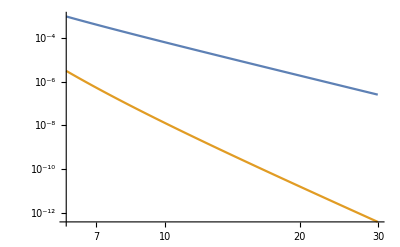

```mathematica
LogLogPlot[{FluxEnergy0PAInfinity[r0],FluxEnergy0PAHorizon[r0]},{r0,rmin0PAFlux,rmax0PAFlux}]
```

### Comparison of interpolating functions

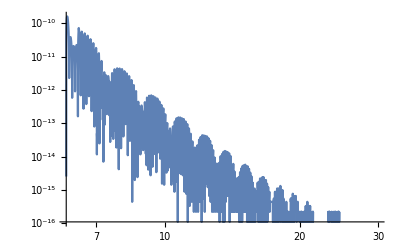

```mathematica
LogLogPlot[Abs[1-FluxEnergy0PAInfinity[r0]/WaSABIFluxEnergy0PAInfinity[r0]],{r0,rmin0PAFlux,rmax0PAFlux}]
```

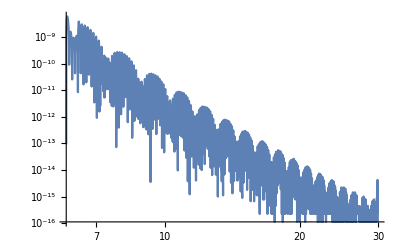

```mathematica
LogLogPlot[Abs[1-FluxEnergy0PAHorizon[r0]/WaSABIFluxEnergy0PAHorizon[r0]],{r0,rmin0PAFlux,rmax0PAFlux}]
```

### Comparison of interpolant against raw WaSABI data

```mathematica
FluxEnergy0PAInfinityRelativeDifferenceOnGrid=({#[[1]], Abs[1 - FluxEnergy0PAInfinity[#[[1]]]/#[[2]]]} & /@ WaSABIFluxEnergy0PAInfinityOnGrid);
```

InterpolatingFunction::dmval: Input value {30.} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
FluxEnergy0PAHorizonRelativeDifferenceOnGrid=({#[[1]], Abs[1 - FluxEnergy0PAHorizon[#[[1]]]/#[[2]]]} & /@ WaSABIFluxEnergy0PAHorizonOnGrid);
```

InterpolatingFunction::dmval: Input value {30.} lies outside the range of data in the interpolating function. Extrapolation will be used.

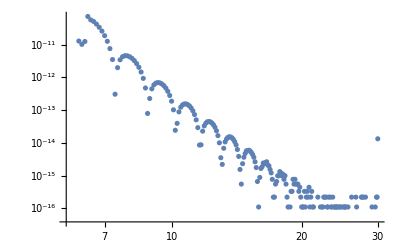

```mathematica
ListLogLogPlot[FluxEnergy0PAInfinityRelativeDifferenceOnGrid]
```

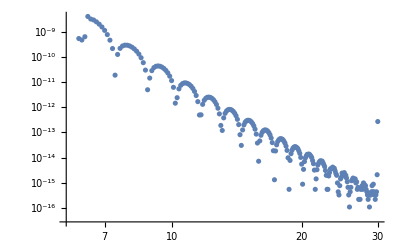

```mathematica
ListLogLogPlot[FluxEnergy0PAHorizonRelativeDifferenceOnGrid]
```

## 0PA angular momentum flux

### Data and interpolants

```mathematica
FluxAngularMomentum0PAGrid=Import[DownloadDirectory<>"Trajectory1PAT1R.h5","Flux/AngularMomentum/0PA/Grid"];
(*FluxAngularMomentum0PAInfinityData=Import[DownloadDirectory<>"Trajectory1PAT1R.h5","Flux/AngularMomentum/0PA/Infinity"];*)
FluxAngularMomentum0PAHorizonData=Import[DownloadDirectory<>"Trajectory1PAT1R.h5","Flux/AngularMomentum/0PA/Horizon"];
```

```mathematica
(*FluxAngularMomentum0PAInfinityOnGrid=Transpose[{FluxAngularMomentum0PAGrid,FluxAngularMomentum0PAInfinityData}];*)
FluxAngularMomentum0PAHorizonOnGrid=Transpose[{FluxAngularMomentum0PAGrid,FluxAngularMomentum0PAHorizonData}];
```

```mathematica
(*FluxAngularMomentum0PAInfinity=Interpolation[FluxAngularMomentum0PAInfinityOnGrid,InterpolationOrder->8];*)
FluxAngularMomentum0PAHorizon=Interpolation[FluxAngularMomentum0PAHorizonOnGrid,InterpolationOrder->8];
```

```mathematica
WaSABIFluxAngularMomentum0PAHorizon[r0_]:=r0^(3/2)WaSABIFluxEnergy0PAHorizon[r0]
```

```mathematica
rminAngularMomentum0PAFlux=FluxAngularMomentum0PAGrid[[1]]
rmaxAngularMomentum0PAFlux=FluxAngularMomentum0PAGrid[[-1]]
```

6.

29.9066

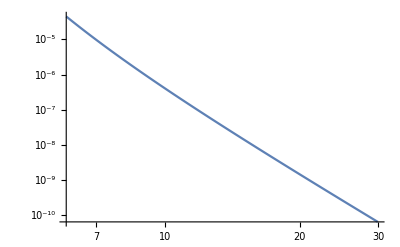

```mathematica
LogLogPlot[FluxAngularMomentum0PAHorizon[r0],{r0,rminAngularMomentum0PAFlux,rmaxAngularMomentum0PAFlux}]
```

### Comparison of interpolating functions

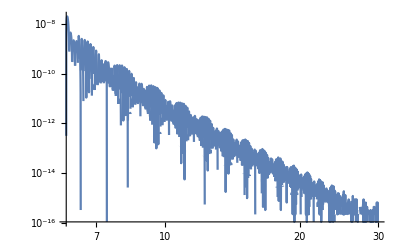

```mathematica
LogLogPlot[Abs[1-FluxAngularMomentum0PAHorizon[r0]/WaSABIFluxAngularMomentum0PAHorizon[r0]],{r0,rmin0PAFlux,rmax0PAFlux}]
```

## 1PA energy flux

### Data and interpolants

```mathematica
FluxEnergy1PAGrid=Import[DownloadDirectory<>"Trajectory1PAT1R.h5","Flux/Energy/1PA/Grid"];
FluxEnergy1PAInfinityData=Import[DownloadDirectory<>"Trajectory1PAT1R.h5","Flux/Energy/1PA/Infinity"];
```

```mathematica
FluxEnergy1PAInfinityOnGrid=Transpose[{FluxEnergy1PAGrid,FluxEnergy1PAInfinityData}];
```

```mathematica
FluxEnergy1PAInfinity=Interpolation[FluxEnergy1PAInfinityOnGrid,InterpolationOrder->8];
FluxEnergy1PAInfinityCubic=Interpolation[FluxEnergy1PAInfinityOnGrid,InterpolationOrder->3];
```

```mathematica
WaSABILogFluxEnergy1PAInfinityOnGrid=Import[Flux1PAdirectory<>"/2SFCircSchwarzDotEInf.m"];
```

```mathematica
WaSABILogFluxEnergy1PAInfinity=Interpolation[WaSABILogFluxEnergy1PAInfinityOnGrid,InterpolationOrder->8];
```

```mathematica
WaSABIFluxEnergy1PAInfinityOnGrid=({Exp[#[[1]]],Re[Exp[#[[2]]]]}& /@ WaSABILogFluxEnergy1PAInfinityOnGrid);
```

```mathematica
WaSABIFluxEnergy1PAInfinity=Function[{r0},Re[Exp[WaSABILogFluxEnergy1PAInfinity[Log[r0]]]]];
```

```mathematica
rmin1PAFlux=FluxEnergy1PAGrid[[1]]
rmax1PAFlux=FluxEnergy1PAGrid[[-1]]
```

6.25

29.9076

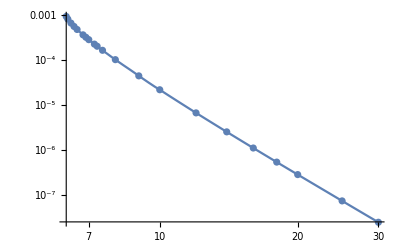

```mathematica
Show[LogLogPlot[-FluxEnergy1PAInfinity[r0],{r0,rmin1PAFlux,rmax1PAFlux}],ListLogLogPlot[Abs[WaSABIFluxEnergy1PAInfinityOnGrid]]]
```

### Comparison of interpolating functions

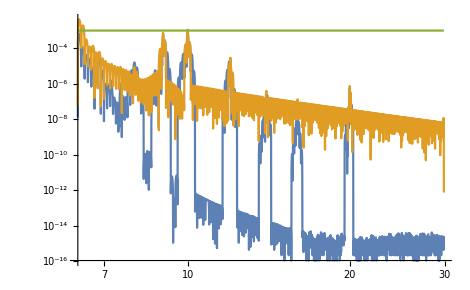

```mathematica
LogLogPlot[{Abs[1-FluxEnergy1PAInfinity[r0]/WaSABIFluxEnergy1PAInfinity[r0]],Abs[1-FluxEnergy1PAInfinityCubic[r0]/WaSABIFluxEnergy1PAInfinity[r0]],.001},{r0,rmin1PAFlux,rmax1PAFlux}]
```

### Comparison of interpolant against raw WaSABI data

```mathematica
WaSABIFluxEnergy1PAInfinityOnGrid
```

{{6.25,-0.000944806},{6.3,-0.000826529},{6.4,-0.000672337},{6.5,-0.000565045},{6.6,-0.000483967},{6.8,-0.00036729},{6.9,-0.000323608},{7.,-0.00028669},{7.2,-0.000228001},{7.3,-0.000204448},{7.5,-0.000165866},{8.,-0.000102583},{9.,-0.000044576},{10.,-0.0000218358},{12.,-6.64667×10^-6},{14.,-2.50638×10^-6},{16.,-1.09236×10^-6},{18.,-5.29534×10^-7},{20.,-2.7868×10^-7},{25.,-7.20794×10^-8},{30.,-2.40403×10^-8},{50.,-1.18434×10^-9}}

```mathematica
FluxEnergy1PAInfinityRelativeDifferenceOnGrid=({#[[1]], Abs[1 - FluxEnergy1PAInfinity[#[[1]]]/#[[2]]]} & /@ WaSABIFluxEnergy1PAInfinityOnGrid);
```

InterpolatingFunction::dmval: Input value {30.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {50.} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
FluxEnergy1PAInfinityCubicRelativeDifferenceOnGrid=({#[[1]], Abs[1 - FluxEnergy1PAInfinityCubic[#[[1]]]/#[[2]]]} & /@ WaSABIFluxEnergy1PAInfinityOnGrid);
```

InterpolatingFunction::dmval: Input value {30.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {50.} lies outside the range of data in the interpolating function. Extrapolation will be used.

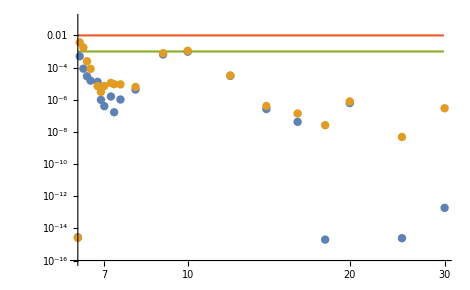

```mathematica
Show[LogLogPlot[{.001,.01},{r0,rmin1PAFlux,rmax1PAFlux},PlotStyle->{ColorData[97,3],ColorData[97,4]},PlotRange->{{rmin1PAFlux,rmax1PAFlux},{10^-16,.1}}],ListLogLogPlot[{FluxEnergy1PAInfinityRelativeDifferenceOnGrid,FluxEnergy1PAInfinityCubicRelativeDifferenceOnGrid}]]
```

## 1PA χ_1 energy flux

### Data and interpolants

```mathematica
FluxEnergy1PAchi1Grid=Import[DownloadDirectory<>"Trajectory1PAT1R.h5","Flux/Energy/1PAchi1/Grid"];
FluxEnergy1PAchi1InfinityData=Import[DownloadDirectory<>"Trajectory1PAT1R.h5","Flux/Energy/1PAchi1/Infinity"];
FluxEnergy1PAchi1HorizonData=Import[DownloadDirectory<>"Trajectory1PAT1R.h5","Flux/Energy/1PAchi1/Horizon"];
```

```mathematica
FluxEnergy1PAchi1InfinityOnGrid=Transpose[{FluxEnergy1PAchi1Grid,FluxEnergy1PAchi1InfinityData}];
FluxEnergy1PAchi1HorizonOnGrid=Transpose[{FluxEnergy1PAchi1Grid,FluxEnergy1PAchi1HorizonData}];
```

```mathematica
FluxEnergy1PAchi1Infinity=Interpolation[FluxEnergy1PAchi1InfinityOnGrid,InterpolationOrder->8];
FluxEnergy1PAchi1Horizon=Interpolation[FluxEnergy1PAchi1HorizonOnGrid,InterpolationOrder->8];
```

```mathematica
WaSABIFluxEnergy1PAchi1InfinityOnGrid=Import[Flux1PAchi1Directory<>"/Slow_chi1_2SFCircSchwarzDotEInf.m"];
```

```mathematica
WaSABIFluxEnergy1PAchi1Infinity=Interpolation[WaSABIFluxEnergy1PAchi1InfinityOnGrid,InterpolationOrder->8];
```

```mathematica
WaSABIFluxEnergy1PAchi1HorizonOnGrid=Import[Flux1PAchi1Directory<>"/Slow_chi1_2SFCircSchwarzDotEHorizon.m"];
```

```mathematica
WaSABIFluxEnergy1PAchi1Horizon=Interpolation[WaSABIFluxEnergy1PAchi1HorizonOnGrid,InterpolationOrder->8];
```

```mathematica
rmin1PAchi1Flux=FluxEnergy1PAchi1Grid[[1]]
rmax1PAchi1Flux=FluxEnergy1PAchi1Grid[[-1]]
```

6.1

29.907

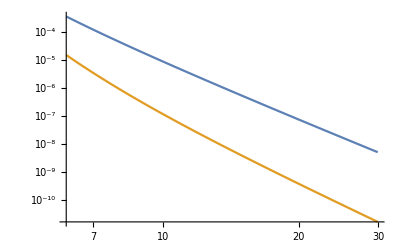

```mathematica
LogLogPlot[{-FluxEnergy1PAchi1Infinity[r0],-FluxEnergy1PAchi1Horizon[r0]},{r0,rmin1PAchi1Flux,rmax1PAchi1Flux}]
```

### Comparison of interpolating functions

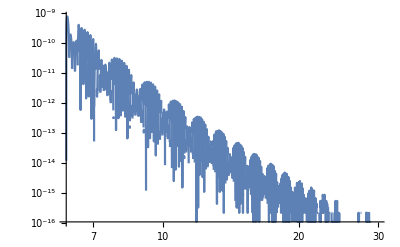

```mathematica
LogLogPlot[Abs[1-FluxEnergy1PAchi1Infinity[r0]/WaSABIFluxEnergy1PAchi1Infinity[r0]],{r0,rmin1PAchi1Flux,rmax1PAchi1Flux}]
```

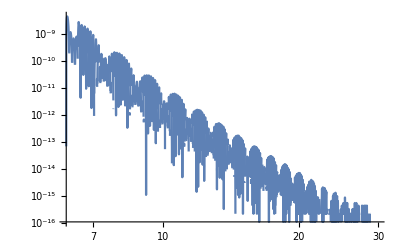

```mathematica
LogLogPlot[Abs[1-FluxEnergy1PAchi1Horizon[r0]/WaSABIFluxEnergy1PAchi1Horizon[r0]],{r0,rmin1PAchi1Flux,rmax1PAchi1Flux}]
```

### Comparison of interpolant against raw WaSABI data

```mathematica
FluxEnergy1PAchi1InfinityRelativeDifferenceOnGrid=({#[[1]], Abs[1 - FluxEnergy1PAchi1Infinity[#[[1]]]/#[[2]]]} & /@ WaSABIFluxEnergy1PAchi1InfinityOnGrid);
```

InterpolatingFunction::dmval: Input value {30} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
FluxEnergy1PAchi1HorizonRelativeDifferenceOnGrid=({#[[1]], Abs[1 - FluxEnergy1PAchi1Horizon[#[[1]]]/#[[2]]]} & /@ WaSABIFluxEnergy1PAchi1HorizonOnGrid);
```

InterpolatingFunction::dmval: Input value {30} lies outside the range of data in the interpolating function. Extrapolation will be used.

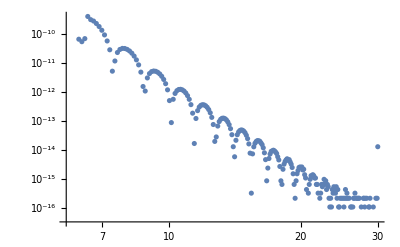

```mathematica
ListLogLogPlot[FluxEnergy1PAchi1InfinityRelativeDifferenceOnGrid]
```

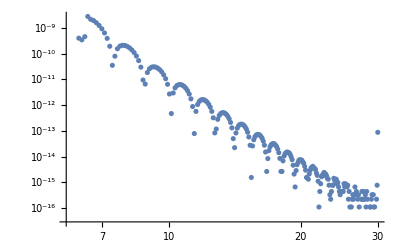

```mathematica
ListLogLogPlot[FluxEnergy1PAchi1HorizonRelativeDifferenceOnGrid]
```

## 1PA χ_2 energy flux

### Data and interpolants

```mathematica
FluxEnergy1PAchi2Grid=Import[DownloadDirectory<>"Trajectory1PAT1R.h5","Flux/Energy/1PAchi2/Grid"];
FluxEnergy1PAchi2InfinityData=Import[DownloadDirectory<>"Trajectory1PAT1R.h5","Flux/Energy/1PAchi2/Infinity"];
FluxEnergy1PAchi2HorizonData=Import[DownloadDirectory<>"Trajectory1PAT1R.h5","Flux/Energy/1PAchi2/Horizon"];
```

```mathematica
FluxEnergy1PAchi2InfinityOnGrid=Transpose[{FluxEnergy1PAchi1Grid,FluxEnergy1PAchi2InfinityData}];
FluxEnergy1PAchi2HorizonOnGrid=Transpose[{FluxEnergy1PAchi2Grid,FluxEnergy1PAchi2HorizonData}];
```

```mathematica
FluxEnergy1PAchi2Infinity=Interpolation[FluxEnergy1PAchi2InfinityOnGrid,InterpolationOrder->8];
FluxEnergy1PAchi2Horizon=Interpolation[FluxEnergy1PAchi2HorizonOnGrid,InterpolationOrder->8];
```

```mathematica
WaSABIFluxEnergy1PAchi2InfinityOnGrid=Import[Flux1PAchi2Directory<>"/chi2_2SFCircSchwarzDotEInf.m"];
```

```mathematica
WaSABIFluxEnergy1PAchi2Infinity=Interpolation[WaSABIFluxEnergy1PAchi2InfinityOnGrid,InterpolationOrder->8];
```

```mathematica
WaSABIFluxEnergy1PAchi2HorizonOnGrid=Import[Flux1PAchi2Directory<>"/chi2_2SFCircSchwarzDotEHorizon.m"];
```

```mathematica
WaSABIFluxEnergy1PAchi2Horizon=Interpolation[WaSABIFluxEnergy1PAchi2HorizonOnGrid,InterpolationOrder->8];
```

```mathematica
rmin1PAchi2Flux=FluxEnergy1PAchi2Grid[[1]]
rmax1PAchi2Flux=FluxEnergy1PAchi2Grid[[-1]]
```

6.1

29.907

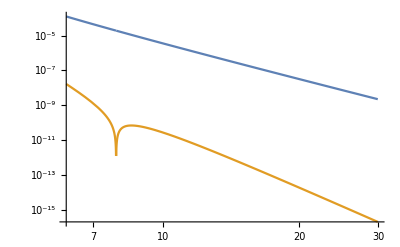

```mathematica
LogLogPlot[{-FluxEnergy1PAchi2Infinity[r0],Abs[FluxEnergy1PAchi2Horizon[r0]]},{r0,6.1,29.9}]
```

### Comparison of interpolating functions

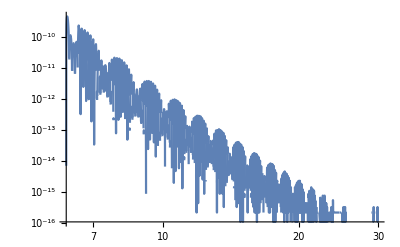

```mathematica
LogLogPlot[Abs[1-FluxEnergy1PAchi2Infinity[r0]/WaSABIFluxEnergy1PAchi2Infinity[r0]],{r0,rmin1PAchi2Flux,rmax1PAchi2Flux}]
```

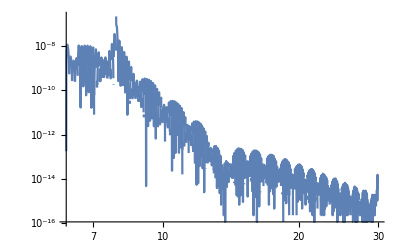

```mathematica
LogLogPlot[Abs[1-FluxEnergy1PAchi2Horizon[r0]/WaSABIFluxEnergy1PAchi2Horizon[r0]],{r0,rmin1PAchi2Flux,rmax1PAchi2Flux}]
```

### Comparison of interpolant against raw WaSABI data

```mathematica
FluxEnergy1PAchi2InfinityRelativeDifferenceOnGrid=({#[[1]], Abs[1 - FluxEnergy1PAchi2Infinity[#[[1]]]/#[[2]]]} & /@ WaSABIFluxEnergy1PAchi2InfinityOnGrid);
```

InterpolatingFunction::dmval: Input value {30} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
FluxEnergy1PAchi2HorizonRelativeDifferenceOnGrid=({#[[1]], Abs[1 - FluxEnergy1PAchi2Horizon[#[[1]]]/#[[2]]]} & /@ WaSABIFluxEnergy1PAchi2HorizonOnGrid);
```

InterpolatingFunction::dmval: Input value {30} lies outside the range of data in the interpolating function. Extrapolation will be used.

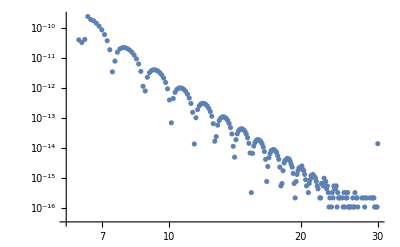

```mathematica
ListLogLogPlot[FluxEnergy1PAchi2InfinityRelativeDifferenceOnGrid]
```

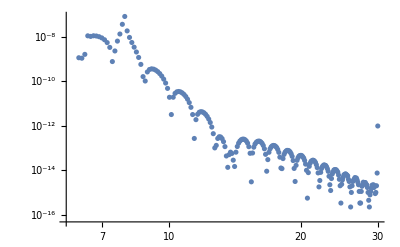

```mathematica
ListLogLogPlot[FluxEnergy1PAchi2HorizonRelativeDifferenceOnGrid]
```